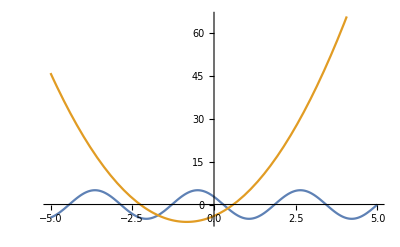

```mathematica
f[x_]:=5Cos[2x+1];g[x_]:=3 x^2+5x-4;
Plot[{f[x],g[x]},{x,-5,5}]
```

```mathematica
a=1;b=2;e=0.001;

x1=b;
Do[x2=x1;
x1=(x1-f[x1]/f'[x1])//N;
If[Abs[x2-x1]<e,
Print["Решение x=",x2//N," получено на ",n," шаге."];
Break[]],
{n,1,100}]
```

Решение x=1.85619 получено на 3 шаге.

```mathematica
ClearAll;
a=1;
b=2;
e=0.001;
max=1000;
i=0;
While[i<max,
f1=f[a];
f2=f[b];
c=a-f1*(b-a)/(f2-f1);
If[Abs[f[c]]<e,Break[]];
If[f1*f[c]<0,b=c,a=c];
i++;
]
N[c,3]
```

1.86